# 教学云端测试与智能分析系统

## 王群勇（教授、博士生导师） 南开大学数量经济研究所

## -Graphics--Graphics- #WolframTechConf

## 摘要

线上教学越来越普及，与之而来的是如何更有效地进行线上测试。本报告介绍在教学过程中如何导入试题库、利用CloudDeploy[]布局云端测试题目，实现对学生答题的智能分析（自动计算分数、成绩的分布、高频错误题目、导出试题分析报告等）。

## 试题库

例：Wooldridge. Introductory Econometrics: A modern approach. chapter 17.

试题库的前两个题目：

```mathematica
StringTake[Import["jw*17.txt"],490]
```

{Chapter 17

1. Which of the following is an example of a binary response model?
a. MA model
b. ARCH model
c. GARCH model
d. Logit model

Answer: d
Difficulty: Easy
Bloom’s: Knowledge
A-Head: Specifying Logit and Probit Models
BUSPROG:
Feedback: The logit model is an example of a binary response model.

2. The model: G(z) = [exp(z)]/[1 + exp(z)],where G is between zero and one for all real numbers ‘z’, represents a:
a. logit model.
b. probit model.
c. Tobit model. 
d. linear probability}

### 导入试题

```mathematica
Needs["Testbank`"]
```

```mathematica
testfiles=FileNames["JW*17.txt"];
ilist={2}; (* 1=判断题，2=单选题，3=多选题，4=分析题 *);
exall=Table[Imquiz[testfiles[[i]]],{i,1,Length[ilist]}];
```

第1题型的第1题：

```mathematica
exall[[1,1]]//TableForm
```

Which of the following is an example of a binary response model? |  |  | 
Nulla. MA modela. MA model→1 | Nullb. ARCH modelb. ARCH model→2 | Nullc. GARCH modelc. GARCH model→3 | Nulld. Logit modeld. Logit model→4
d |  |  |

### 将题目转换为Form的形式

```mathematica
fdef=TbForm[exall,ilist];
```

## 云端部署

创建云端数据仓库：

```mathematica
(* create databin *)
dbid=CreateDatabin[<|"Name"->"dbjw17",Permissions->"Public"|>]
```

Databin[…]

```mathematica
(* 直接指定数据仓库 *)
dbid="UGvFwzkk";
```

创建FormFunction[]：

```mathematica
ffunc=FormFunction[Flatten@fdef,
(DatabinAdd[dbid,{Apply[Sequence,##],CurrentDate[]}];
Panel@Grid[{{Style["姓名",Medium,Black],Values[#names][[1]]},
{Style["提交时间",Medium,Black],DateString[CurrentDate[]]},{ Style["Thank you!",Large,Black],SpanFromLeft}}, Alignment->Center,Frame->All,Dividers->{{True},{True,True,True}},ItemSize->{{5,5}},Spacings->{1,2}])&,
AppearanceRules-><|"Title"->"Econometrics",
"Description"->"Limited dependent variable model",
"ItemLayout" -> "Vertical"|>];
```

然后将试题部署到云端：

```mathematica
CloudDeploy[ffunc,"jw17",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/brynewqy/jw17]

```mathematica
WebImage["https://www.wolframcloud.com/obj/brynewqy/jw17"]
```

-Graphics-

## 智能分析

从云端下载答题情况：

```mathematica
(* databin id *)
dbid="UGvFwzkk";
(* restric time range *)
start={2021,4,10,13,0,0};
deadline={2021,4,15,15,0,0};
```

```mathematica
wqy=Databin[dbid]
```

Databin[…]

```mathematica
oresult=Values[wqy];
```

```mathematica
Length[oresult]
```

38

```mathematica
(* export the original data *)
Export["jw17.mx",oresult]
```

econ-1.mx

### 答题

```mathematica
cans=TbAnsw[testfiles];
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
D | A | C | D | D | C | B | A | B | C | D | B | B | C | C | B | B | A | A | B

### 答题情况

```mathematica
stuansw=TbStuAnsw[dbid,cans, start,deadline];
```

姓名 | 学号 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 提交时间
 | 答案 | D | A | C | D | D | C | B | A | B | C | D | B | B | C | C | B | B | A | A | B | 
秦旭 | 1810479 | D | A | C | D | D | C | B | D | B | C | D | B | B | C | C | B | B | A | A | B | 14:00 April 12, 2021
王子健 | 1812304 | D | B | B | D | D | C | C | A | C | C | D | C | D | C | C | B | B | A | A | B | 14:01 April 12, 2021
赵海桥 | 1811240 | D | D | D | D | D | B | B | B | C | C | B | C | D | D | B | B | A | A | B | A | 14:02 April 12, 2021
郝宇 | 1811544 | D | A | C | D | D | C | B | A | B | C | D | B | C | D | C | B | B | A | A | B | 14:03 April 12, 2021
王士元 | 1812673 | D | A | C | D | D | C | B | A | B | C | D | D | B | D | C | B | A | A | A | B | 14:05 April 12, 2021
孙尧 | 1810834 | D | A | C | D | D | C | B | A | B | C | D | B | B | C | C | B | B | A | A | B | 14:15 April 12, 2021
沈孟京 | 1811416 | D | A | C | D | D | C | B | A | B | C | D | B | C | C | C | B | B | A | A | B | 14:13 April 12, 2021
王睿琦 | 1812036 | D | A | C | D | D | C | B | A | B | C | D | B | B | C | C | B | B | A | A | B | 14:18 April 12, 2021
唐立 | 1812028 | D | A | C | D | D | C | B | A | B | C | D | B | B | A | C | B | A | A | B | A | 14:15 April 12, 2021
陈佳星 | 1811968 | D | A | C | D | D | C | B | A | C | C | D | B | C | D | C | B | B | A | A | B | 14:16 April 12, 2021
姜安然 | 1813637 | D | A | C | D | D | C | B | A | B | C | D | C | B | D | C | B | A | A | A | B | 14:16 April 12, 2021
郭子豪 | 1811985 | D | A | C | D | D | C | B | A | C | C | D | B | C | D | C | B | B | A | A | B | 14:16 April 12, 2021
徐海滔 | 1811020 | D | A | C | D | D | C | A | A | A | C | D | C | B | D | C | B | B | A | A | B | 14:17 April 12, 2021
蔡沁晨 | 1811529 | D | A | C | D | D | C | B | A | B | C | D | B | C | D | C | B | B | A | A | B | 14:17 April 12, 2021
祝嘉佳 | 1812072 | D | A | C | D | D | C | B | A | A | C | D | C | B | D | C | B | A | A | B | B | 14:18 April 12, 2021
赵熙鹏 | 1810714 | D | A | A | D | D | D | B | A | C | C | D | B | B | C | C | B | A | A | A | B | 14:20 April 12, 2021
朱辉 | 1813668 | D | A | C | D | D | C | B | A | C | C | D | B | B | C | C | B | A | B | A | B | 14:19 April 12, 2021
李明泽 | 1810681 | D | A | C | D | D | C | B | A | C | C | D | B | B | A | C | B | A | A | A | B | 14:19 April 12, 2021
赵宇晖 | 1810327 | D | A | C | D | D | C | B | A | A | C | D | B | B | C | C | B | B | A | A | B | 14:19 April 12, 2021
刘入源 | 1810686 | D | A | C | D | D | C | D | A | B | C | D | B | C | C | C | B | A | A | A | B | 14:20 April 12, 2021
律烨琳 | 1812444 | D | A | C | D | D | C | B | A | A | C | B | B | B | B | C | A | A | A | A | B | 14:21 April 12, 2021
金子涵 | 1811993 | D | A | C | D | D | C | B | A | B | C | D | B | C | D | C | B | B | A | A | B | 14:22 April 12, 2021
张思益 | 1812212 | D | A | C | D | D | C | B | A | B | C | D | B | C | D | C | B | B | A | A | B | 14:23 April 12, 2021
高哲铭 | 1811357 | D | A | C | D | D | C | B | A | C | C | D | B | B | C | C | B | A | A | A | B | 14:24 April 12, 2021
郭铭玥 | 1812576 | D | A | C | D | D | D | D | A | B | C | D | B | B | B | C | B | B | A | B | A | 14:25 April 12, 2021
边疆 | 1811032 | D | A | C | D | D | C | B | A | B | C | D | B | B | C | D | B | B | A | A | B | 14:32 April 12, 2021
高凌波 | 1813067 | D | A | A | D | D | C | B | A | B | C | D | D | B | D | C | B | B | A | A | B | 14:49 April 12, 2021
胡翔川 | 1813855 | D | A | C | D | D | C | B | A | B | C | D | B | B | C | C | B | A | A | A | B | 16:28 April 12, 2021

### 得分

```mathematica
scoretable=TbScore[stuansw, cans, {5}, {20}];
```

提交序号 | 姓名 | 学号 | 正确个数 | 得分
8 | 王睿琦 | 1812036 | 20 | 100.
6 | 孙尧 | 1810834 | 20 | 100.
28 | 胡翔川 | 1813855 | 19 | 95.
26 | 边疆 | 1811032 | 19 | 95.
19 | 赵宇晖 | 1810327 | 19 | 95.
7 | 沈孟京 | 1811416 | 19 | 95.
1 | 秦旭 | 1810479 | 19 | 95.
24 | 高哲铭 | 1811357 | 18 | 90.
23 | 张思益 | 1812212 | 18 | 90.
22 | 金子涵 | 1811993 | 18 | 90.
14 | 蔡沁晨 | 1811529 | 18 | 90.
4 | 郝宇 | 1811544 | 18 | 90.
27 | 高凌波 | 1813067 | 17 | 85.
20 | 刘入源 | 1810686 | 17 | 85.
18 | 李明泽 | 1810681 | 17 | 85.
17 | 朱辉 | 1813668 | 17 | 85.
12 | 郭子豪 | 1811985 | 17 | 85.
11 | 姜安然 | 1813637 | 17 | 85.
10 | 陈佳星 | 1811968 | 17 | 85.
5 | 王士元 | 1812673 | 17 | 85.
16 | 赵熙鹏 | 1810714 | 16 | 80.
13 | 徐海滔 | 1811020 | 16 | 80.
9 | 唐立 | 1812028 | 16 | 80.
25 | 郭铭玥 | 1812576 | 15 | 75.
21 | 律烨琳 | 1812444 | 15 | 75.
15 | 祝嘉佳 | 1812072 | 15 | 75.
2 | 王子健 | 1812304 | 14 | 70.
3 | 赵海桥 | 1811240 | 7 | 35.

```mathematica
Export["econ-1.xlsx",scoretable];
```

### 统计分析

直方图：

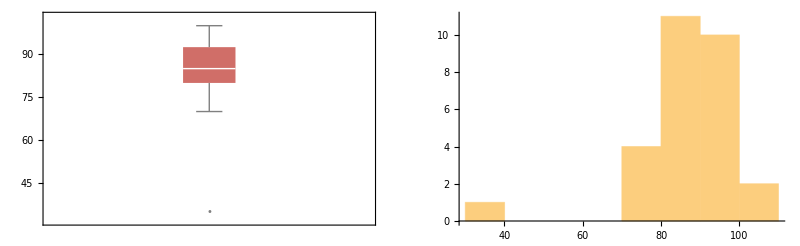

```mathematica
TbGraphics[scoretable[[2;;-1,-1]]]
```

基本统计指标：

```mathematica
stat=TbStat[scoretable[[2;;-1,-1]]];
```

人数 | 平均分 | 中位数 | 最低分 | 最高分 | <60分 | >=90分
28. | 84.8 | 85. | 35. | 100. | 1. | 12.

#### 高频错误题目

```mathematica
errtab=TbErrtab[stuansw,cans];
```

```mathematica
Dimensions[exall]
```

{1,20,3}

```mathematica
cobj=CloudDeploy[TabView[Table[c=#1[[i,1]];c->Style[Grid[Prepend[{{#1[[i,2]],Column@Join[{#2[[c,1]]},Keys[#2[[c,2]]]],#2[[c,3]]}},{"正确率","题目","答案"}],Frame->All,Alignment->{Left,Top},ItemSize->{{4,30,4}}],{12}],
{i,1,Length[#1]}],ControlPlacement->Left]&[errtab[[1;;10,All]],exall[[1]]]]
```

CloudObject[https://www.wolframcloud.com/obj/21f91d90-407f-43e3-a5ac-bc23ecc78830]

```mathematica
WebImage["https://www.wolframcloud.com/obj/21f91d90-407f-43e3-a5ac-bc23ecc78830"]
```

#### 未来的扩展

自动初建分析报告。

将题目分为难度为低、中、高不同的级别。

随机选择题目。

设置学生信息库，限定特定班级的学生进入测试。

限定答题时间。

学生可以实时下载所需的数据，进行计量分析。

## 谢谢，欢迎批评指正！